```mathematica
SetDirectory[NotebookDirectory[]];
<<CIP`CurveFit`
```

# V7 - Auswertung

### Import aller Messdaten

```mathematica
rawData=Import["C:\\Users\\hannah\\github_repos\\THERMO-EDA\\v7\\v7_messdaten.csv"]
trawData=Import["C:\\Users\\hannah\\github_repos\\THERMO-EDA\\v7\\Adsorption.csv"]
```

{{c0,V,VHAc},{0.05,5.3,20},{0.05,5.1,20},{0.05,5.1,20},{0.1,29.6,20},{0.1,29.,20},{0.1,29.6,20},{0.2,24.9,10},{0.2,24.,10},{0.2,23.,10},{0.3,13.3,6},{0.3,12.8,6},{0.3,13.,6},{0.5,18.5,4},{0.5,19.1,4},{0.5,18.2,4},{0.8,19.1,2.5},{0.8,21.6,2.5},{0.8,20.6,2.5}}

{{Konz [mol / l],V Titriert [ml],V Vorgelegt [ml],A Kohle [g]},{0.8,16.2,3,1.0025},{0.8,16.,3,1.0025},{0.8,16.4,3,1.0025},{0.5,13.6,4,1.0021},{0.5,13.8,4,1.0021},{0.5,13.4,4,1.0021},{0.3,13,7,1.003},{0.3,13,9,1.003},{0.3,13,5,1.003},{0.2,12.1,10,1.0021},{0.2,12.3,10,1.0021},{0.2,12.,10,1.0021},{0.1,11.1,20,1.0007},{0.1,11.3,20,1.0007},{0.1,11.,20,1.0007},{0.05,9.,40,1.0001},{0.05,9.2,40,1.0001},{0.05,9.4,40,1.0001}}

```mathematica
rawDataT=Transpose[Drop[rawData,1]]
```

{{0.05,0.05,0.05,0.1,0.1,0.1,0.2,0.2,0.2,0.3,0.3,0.3,0.5,0.5,0.5,0.8,0.8,0.8},{5.3,5.1,5.1,29.6,29.,29.6,24.9,24.,23.,13.3,12.8,13.,18.5,19.1,18.2,19.1,21.6,20.6},{20,20,20,20,20,20,10,10,10,6,6,6,4,4,4,2.5,2.5,2.5}}

### Bestimmung der Gleichgewichtskonzentration

```mathematica
cg[c_,V_]:=c/V
```

```mathematica
cgRawData=Map[cg[0.1,#]&,rawDataT[[2]]];
```

```mathematica
cgDataLangmuir=1/cgRawData;
cgDataFreundlich=Log10[cgRawData];
```

### Bestimmung der Adsorptionsmolalität

```mathematica
mAd[c0_,cg_,VHAc_]:=(c0-cg)/VHAc
```

```mathematica
mAdData={};
For[i=2,i<=Length[rawData],i++,
AppendTo[
mAdData,
mAd[rawData[[i,1]],cgRawData[[i-1]],rawData[[i,3]]]
];
];
mAdDataLangmuir=1/mAdData
mAdDataFreundlich=Log10[mAdData]
```

{642.424,658.065,658.065,206.993,207.143,206.993,51.0246,51.0638,51.1111,20.5141,20.5348,20.5263,8.08743,8.08466,8.08889,3.14559,3.14319,3.14408}

{-2.80782,-2.81827,-2.81827,-2.31596,-2.31627,-2.31596,-1.70778,-1.70811,-1.70852,-1.31205,-1.31249,-1.31231,-0.907811,-0.907662,-0.907889,-0.497702,-0.497371,-0.497493}

### X, Y - Liste

#### Berechnung der Mittelwerte

```mathematica
cgMeanDataLangmuir=Map[Mean[#]&,Partition[cgDataLangmuir,3]]
cgMeanDataFreundlich=Map[Mean[#]&,Partition[cgDataFreundlich,3]]
mAdMeanDataLangmuir=Map[Mean[#]&,Partition[mAdDataLangmuir,3]]
mAdMeanDataFreundlich=Map[Mean[#]&,Partition[mAdDataFreundlich,3]]
```

{51.6667,294.,239.667,130.333,186.,204.333}

{-1.71314,-2.46833,-2.37938,-2.115,-2.26943,-2.30978}

{652.851,207.043,51.0665,20.5251,8.08699,3.14428}

{-2.81479,-2.31606,-1.70814,-1.31228,-0.907787,-0.497522}

#### Berechnung der Standardabweichungen

```mathematica
cgSdDataLangmuir=Map[StandardDeviation[#]&,Partition[cgDataLangmuir,3]]
cgSdDataFreundlich=Map[StandardDeviation[#]&,Partition[cgDataFreundlich,3]]
mAdSdDataLangmuir=Map[StandardDeviation[#]&,Partition[mAdDataLangmuir,3]]
mAdSdDataFreundlich=Map[StandardDeviation[#]&,Partition[mAdDataFreundlich,3]]
```

{1.1547,3.4641,9.50438,2.51661,4.58258,12.5831}

{0.00964504,0.00513479,0.0172508,0.00837116,0.0106612,0.0269432}

{9.02992,0.086516,0.0433227,0.0103664,0.00215035,0.00121155}

{0.00603132,0.000181455,0.000368423,0.000219356,0.000115484,0.000167334}

### CIP Integration für Langmuir-Modell

```mathematica
xyErrorTriple1L={cgMeanDataLangmuir[[1]],mAdMeanDataLangmuir[[1]],mAdSdDataLangmuir[[1]]};
xyErrorTriple2L={cgMeanDataLangmuir[[2]],mAdMeanDataLangmuir[[2]],mAdSdDataLangmuir[[2]]};
xyErrorTriple3L={cgMeanDataLangmuir[[3]],mAdMeanDataLangmuir[[3]],mAdSdDataLangmuir[[3]]};
xyErrorTriple4L={cgMeanDataLangmuir[[4]],mAdMeanDataLangmuir[[4]],mAdSdDataLangmuir[[4]]};
xyErrorTriple5L={cgMeanDataLangmuir[[5]],mAdMeanDataLangmuir[[5]],mAdSdDataLangmuir[[5]]};
xyErrorTriple6L={cgMeanDataLangmuir[[6]],mAdMeanDataLangmuir[[6]],mAdSdDataLangmuir[[6]]};
xyErrorTripleDataL={xyErrorTriple1L,xyErrorTriple2L,xyErrorTriple3L,xyErrorTriple4L,xyErrorTriple5L,xyErrorTriple6L};
```

{{130.333,20.5251,0.0103664},{186.,8.08699,0.00215035},{204.333,3.14428,0.00121155}}

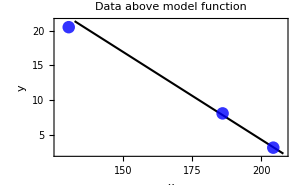

54.9184-0.253095 x

Root mean squared error (RMSE) = 8.249×10^-1

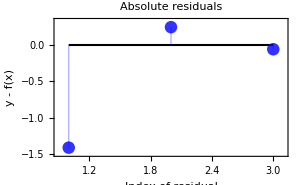

Standard deviation of fit = 3.336×10^-1

Out 1 : Correlation coefficient = 0.999223

```mathematica
xyErrorTripleDataL={xyErrorTriple4L,xyErrorTriple5L,xyErrorTriple6L}
modelFunction=a x+b;
argumentOfModelFunction=x;
parametersOfModelFunction={a,b};
curveFitInfoModel=CIP`CurveFit`FitModelFunction[
xyErrorTripleDataL,
modelFunction,
argumentOfModelFunction,
parametersOfModelFunction];
CIP`CurveFit`ShowFitResult[
{"FunctionPlot","ModelFunction","RMSE"},
xyErrorTripleDataL,
curveFitInfoModel]
CIP`CurveFit`ShowFitResult[
{"AbsoluteResidualsPlot","SDFit","CorrelationCoefficient"},
xyErrorTripleDataL,
curveFitInfoModel]
```

```mathematica
mAdMax=1/54.918372379809476
b=1/(-0.25309502726023575*mAdMax)
```

0.0182088

-216.987

m_ad_max = 0,0182088
b = -216.987
R^2 = 0,999223
“Ausreißer” : 0.05; 0,1; 0,2

### CIP Integration für Freundlich - Modell

```mathematica
xyErrorTriple1F={cgMeanDataFreundlich[[1]],mAdMeanDataFreundlich[[1]],mAdSdDataFreundlich[[1]]};
xyErrorTriple2F={cgMeanDataFreundlich[[2]],mAdMeanDataFreundlich[[2]],mAdSdDataFreundlich[[2]]};
xyErrorTriple3F={cgMeanDataFreundlich[[3]],mAdMeanDataFreundlich[[3]],mAdSdDataFreundlich[[3]]};
xyErrorTriple4F={cgMeanDataFreundlich[[4]],mAdMeanDataFreundlich[[4]],mAdSdDataFreundlich[[4]]};
xyErrorTriple5F={cgMeanDataFreundlich[[5]],mAdMeanDataFreundlich[[5]],mAdSdDataFreundlich[[5]]};
xyErrorTriple6F={cgMeanDataFreundlich[[6]],mAdMeanDataFreundlich[[6]],mAdSdDataFreundlich[[6]]};
xyErrorTripleDataF={xyErrorTriple1F,xyErrorTriple2F,xyErrorTriple3F,xyErrorTriple4F,xyErrorTriple5F,xyErrorTriple6F};
```

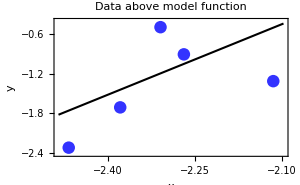

6.98589+3.54186 x

Root mean squared error (RMSE) = 5.555×10^-1

```mathematica
xyErrorTripleDataF={xyErrorTriple2F,xyErrorTriple3F,xyErrorTriple4F,xyErrorTriple5F,xyErrorTriple6F};
modelFunction=a x+b;
argumentOfModelFunction=x;
parametersOfModelFunction={a,b};
curveFitInfoModel=CIP`CurveFit`FitModelFunction[
xyErrorTripleDataF,
modelFunction,
argumentOfModelFunction,
parametersOfModelFunction];
CIP`CurveFit`ShowFitResult[
{"FunctionPlot","ModelFunction","RMSE"},
xyErrorTripleDataF,
curveFitInfoModel]
```

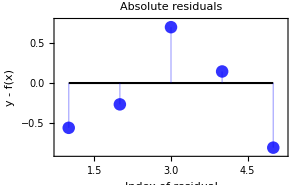

Standard deviation of fit = 6.47×10^-1

Out 1 : Correlation coefficient = 0.547082

```mathematica
CIP`CurveFit`ShowFitResult[
{"AbsoluteResidualsPlot","SDFit","CorrelationCoefficient"},
xyErrorTripleDataF,
curveFitInfoModel]
```

```mathematica
nF=1/6.9858915188374695
KFPrime=10^3.541858745231209
```

0.143146

3482.24

n_F = 0.143146
K_F’ = 3482.24
R^2 = 0.547082
“Ausreißer” : 0.05